# Quantum Noise NIN and NIS for T1 = 3-ΔT/2K, T2 = 3+ΔT/2K as a function of Z for applied voltage bias V = 0.000

```mathematica
T1=3-T/2;
T2=3+T/2;
A=(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2));

(* -((2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z))) *)

B=-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2));
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 
Bn=1/(1+Z^2);
kb=8.615*10^-5;
Tc=9.2; 
ds=1.764*kb*Tc;  
Ef=100*ds;
d=1;
a1=kb*T2;
T=0.5;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0000;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
cond1=NIntegrate[(1-Abs[B]^2+Abs[A]^2)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
cond2=NIntegrate[(Bn)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
list=AppendTo[list1,{Z,(2*Re[Qth11NS]+2*Re[Qsh11NS])/(3*kb),(2*Re[Qth11NN]+2*Re[Qsh11NN])/(3*kb),2*Re[Qsh11NS]/(3*kb),2*Re[Qsh11NN]/(3*kb),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN]),Re[Qsh11NS]/(3*kb*cond1),Re[Qsh11NN]/(3*kb*cond2),(2*Re[Qsh11NS]/(3*kb))/(2*Re[Qsh11NN]/(3*kb)),(Re[Qsh11NS]/(3*kb*cond1))/(Re[Qsh11NN]/(3*kb*cond2))}];
},{Z,0.0165,4.0165,0.05}];//AbsoluteTiming
listn=Sort[list1];
Export["QT1.dat",listn]
```

{25.1933,Null}

QT1.dat

#### Check

```mathematica
T1=3-T/2;
T2=3+T/2;
A=(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2));

(* -((2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z))) *)

B=-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2));
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 
Bn=1/(1+Z^2);
kb=8.615*10^-5;
Tc=9.2; 
ds=1.764*kb*Tc; (* 1.4meV*)
Ef=100*ds;
d=1;
a1=kb*T2;
T=0.5;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
V1=0.0000;
Z=0.0165;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
cond1=NIntegrate[(1-Abs[B]^2+Abs[A]^2)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
cond2=NIntegrate[(Bn)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
(2*Re[Qsh11NS]/(3*kb))/(2*Re[Qsh11NN]/(3*kb))
```

16.0815

## Quantum noise correlation for NIN as a function of Z

```mathematica
dataQn0c=Import["QT01.dat"][[All,{1,3}]];
dataQn1c=Import["QT1.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
```

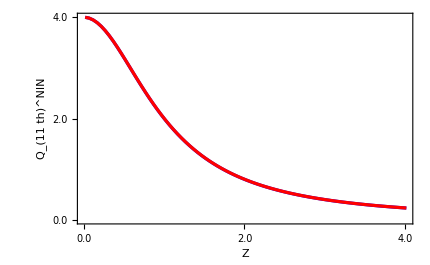

```mathematica
Qn=ListLinePlot[{dataQn0c,dataQn1c},Frame->True,PlotRange->All,Frame->True,
FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{2.0,"2.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},
FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  th)^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

## Quantum noise correlation for NIS as a function of Z

```mathematica
dataQs0c=Import["QT01.dat"][[All,{1,2}]];
dataQs1c=Import["QT1.dat"][[All,{1,2}]];
```

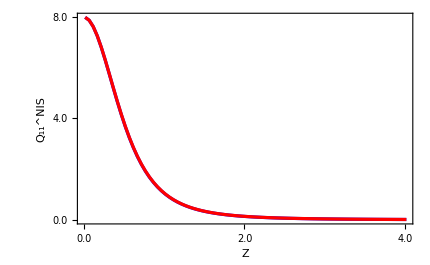

```mathematica
Qs=ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->All,Frame->True,FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},FrameLabel->{Style["Z",19,Bold,Black],Style["Q_11^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->{0,8.1},Frame->True,
PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},Scaled[{0.8,0.15}] ],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  th)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qn,Scaled[{0.5,0.5}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

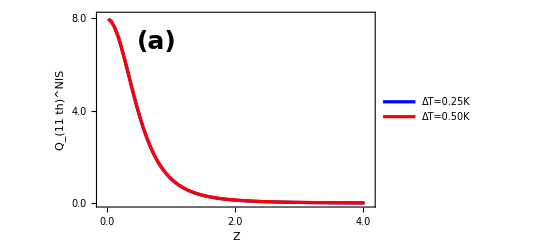
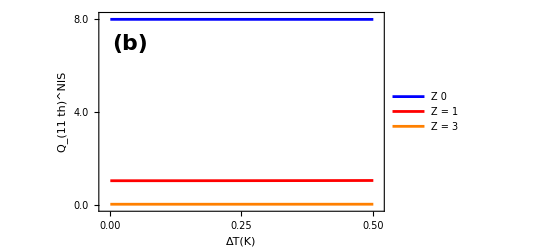

## Δ_T noise in NIN

```mathematica
dataQsh0nc=Import["QT01.dat"][[All,{1,5}]];
dataQsh1nc=Import["QT1.dat"][[All,{1,5}]];
```

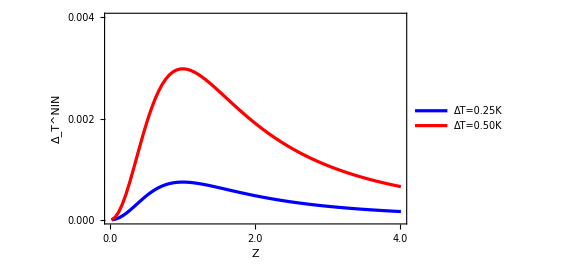

```mathematica
ListLinePlot[{dataQsh0nc,dataQsh1nc},Frame->True,PlotRange->{0,0.004},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Style["Δ_T^NIN",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.0,"0.000"},{0.004,"0.004"},{0.01,"0.01"},{0.002,"0.002"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{dataQsh0nc,dataQsh1nc},Frame->True,PlotRange->{0,0.004},Frame->True,
PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},Scaled[{0.3,0.3}] ],FrameLabel->{Style["Z",19,Bold,Black],Style[Subsuperscript["Δ", T, "NIN"],19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.000"},{0.002,"0.002"},{0.004,"0.004"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qn,Scaled[{0.6,0.55}],Scaled[{0,0}],2.4],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

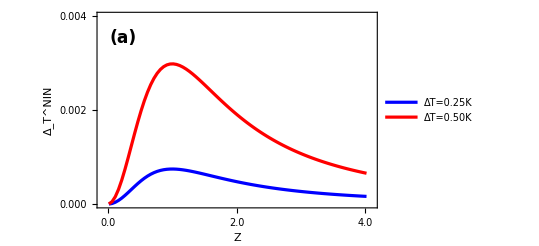
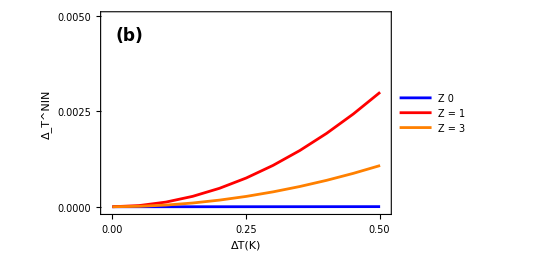

## Δ_T noise in NIS

```mathematica
dataQsh0c=Import["QT01.dat"][[All,{1,4}]];
dataQsh1c=Import["QT1.dat"][[All,{1,4}]];
```

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->All,Frame->True,PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.5K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",25,Bold,Black],Style["Δ_T^NIS",25,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.000"},{0.006,"0.006"},{0.012,"0.012"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

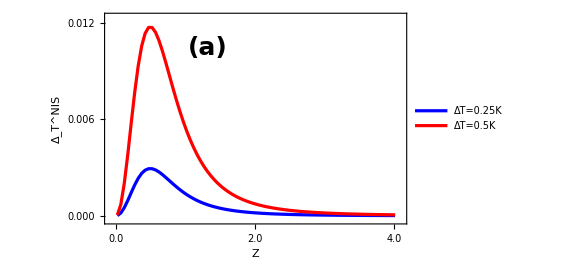

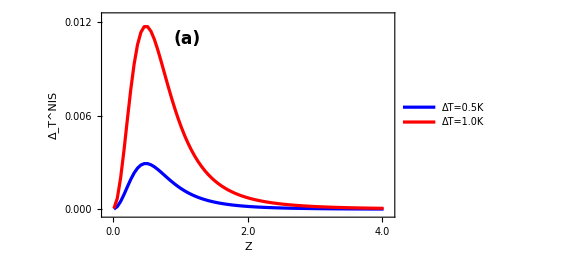
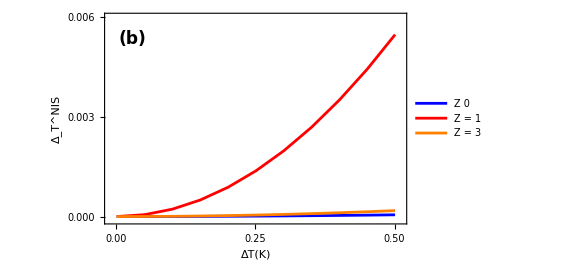

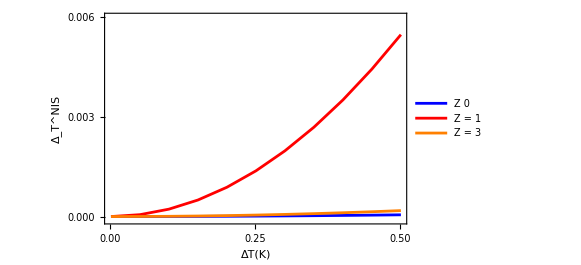

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{0,0.013},Frame->True,
PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},Scaled[{0.8,0.15}] ],FrameLabel->{Style["Z",19,Bold,Black],Style[Subsuperscript["Δ", T, "NIS"],19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.000"},{0.006,"0.006"},{0.012,"0.012"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qs,Scaled[{0.5,0.5}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

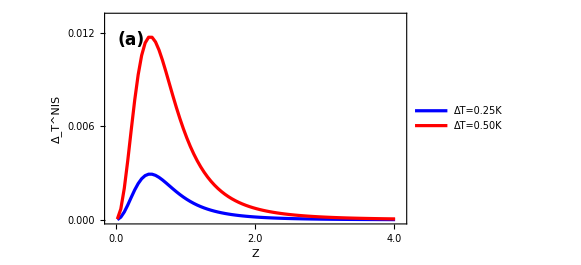
```mathematica
-Graphics-□
```

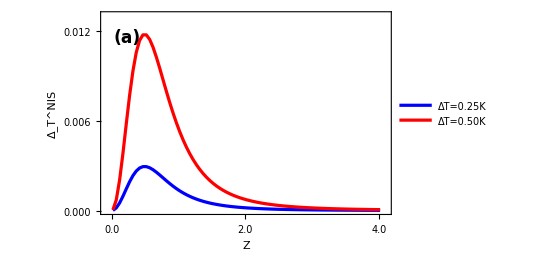
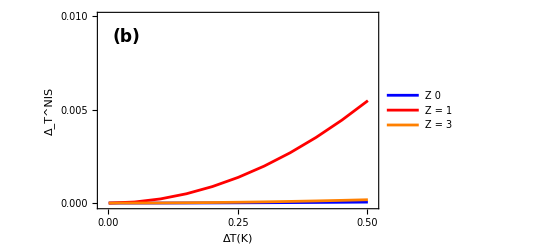

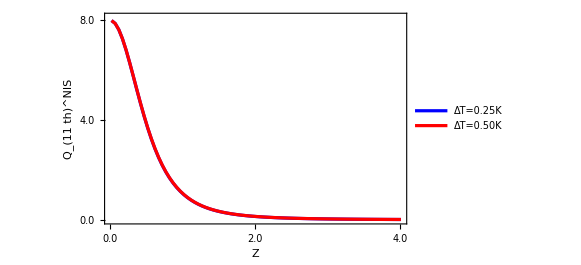

```mathematica
ListLinePlot[{dataQs0c,dataQs1c},Frame->True,PlotRange->{0,8.1},Frame->True,
PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},Scaled[{0.8,0.15}] ],FrameLabel->{Style["Z",19,Bold,Black],Style["Q_(11  th)^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Red]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[Qn,Scaled[{0.5,0.5}],Scaled[{0,0}],2.75],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

## Δ_T /G in NIS

```mathematica
dataQsh0c=Import["QT01.dat"][[All,{1,7}]];
dataQsh1c=Import["QT1.dat"][[All,{1,7}]];
```

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{0,0.012},Frame->True,PlotLegends->Placed[{Style["ΔT=0.25K",22,Black,Bold],Style["ΔT=0.50K",22,Black,Bold]},{Right,Bottom}],FrameLabel->{Style["Z",25,Bold,Black],Rotate[Style["(Δ̄)_T^NIS",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],FrameTicks->{{{{0.0,"0.000"},{0.006,"0.006"},{0.012,"0.012"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->750,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[DGsT,Scaled[{0.4,0.4}],Scaled[{0,0}],2.3],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

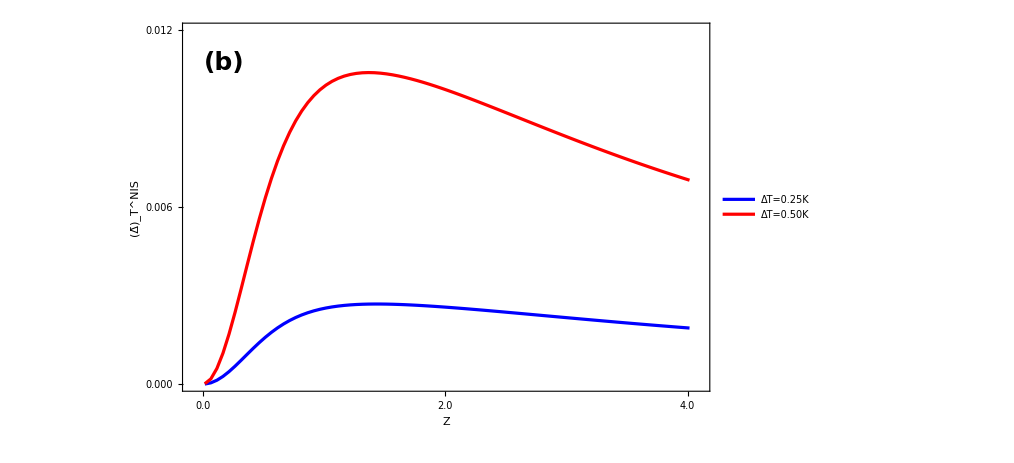

## Δ_T^NIN /G=(Δ̄)_T^NIN

```mathematica
dataQsh0c=Import["QT01.dat"][[All,{1,8}]];
dataQsh1c=Import["QT1.dat"][[All,{1,8}]];
```

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{0,0.006},Frame->True,PlotLegends->Placed[{Style["ΔT=0.25K",22,Black,Bold],Style["ΔT=0.50K",22,Black,Bold]},Scaled[{0.8,0.1}] ],FrameLabel->{Style["Z",25,Bold,Black],Rotate[Style["(Δ̄)_T^NIN",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22],FrameTicks->{{{{0.0,"0.000"},{0.006,"0.006"},{0.003,"0.003"},{0.02,"0.02"}},None},{{{0,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},ImageSize->750,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[DGnT,Scaled[{0.6,0.4}],Scaled[{0,0}],2.55],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

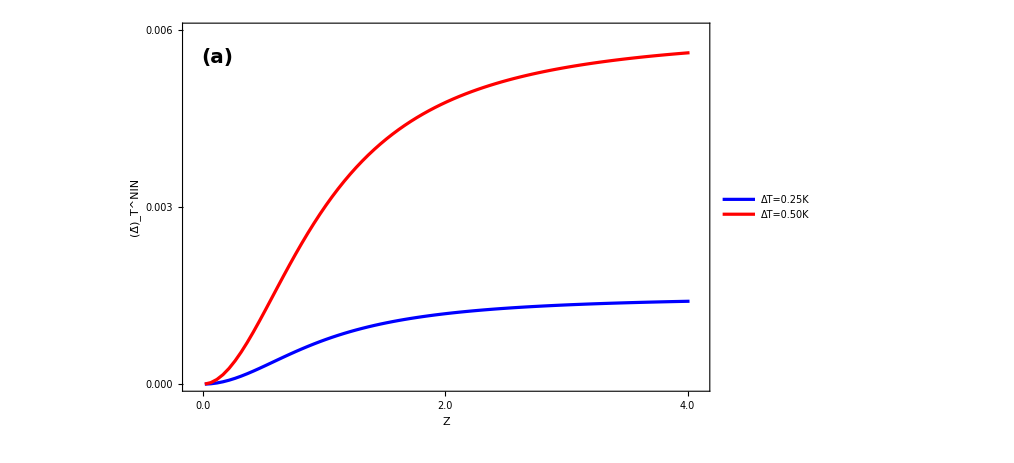

## Δ_T^NIS/Δ_T^NIN

```mathematica
dataQsh0c=Import["QT01.dat"][[All,{1,9}]];
dataQsh1c=Import["QT1.dat"][[All,{1,9}]];
```

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{{0.0165,4},{0,16.5}},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",19,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,19,Thick],PlotLegends->Placed[{Style["ΔT=0.25K",19,Black,Bold],Style["ΔT=0.50K",19,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.01,"0.0"},{20.06,"0.06"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0.0165,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},ImageSize->430,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

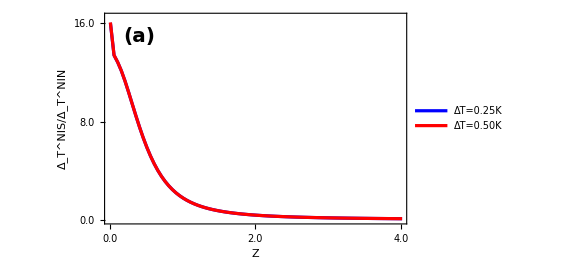

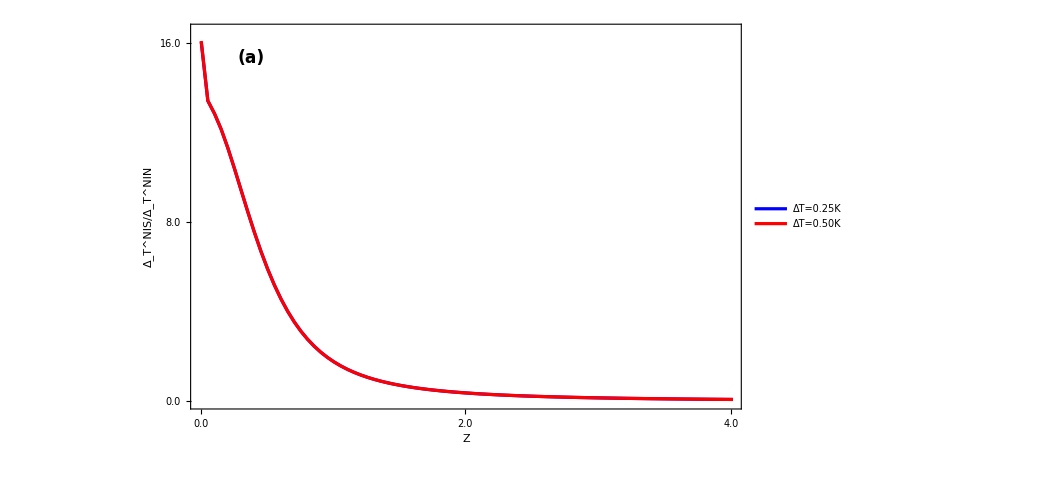

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{{0.0165,4},{0,16.5}},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],PlotLegends->Placed[{Style["ΔT=0.25K",22,Black,Bold],Style["ΔT=0.50K",22,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.01,"0.0"},{20.06,"0.06"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0.0165,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},ImageSize->750,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[rdt,Scaled[{0.4,0.3}],Scaled[{0,0}],2.55],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

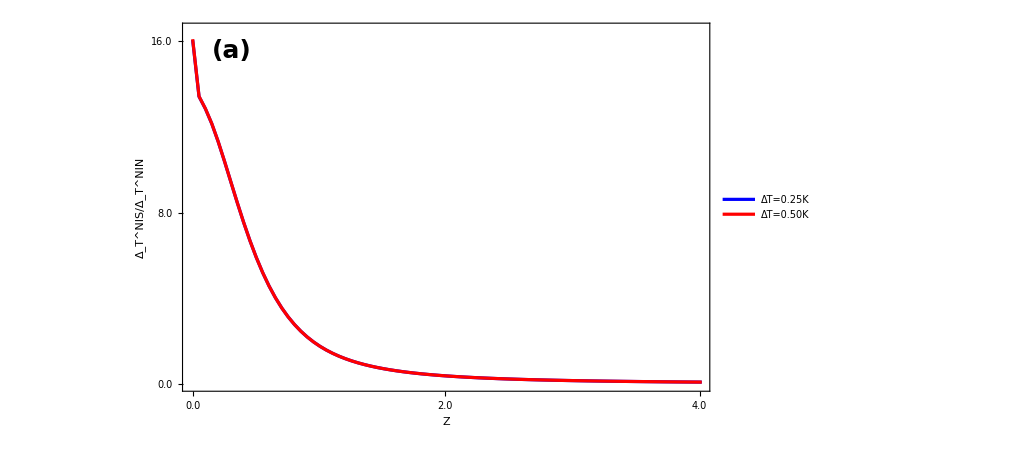

## (Δ̄)_T^NIS/(Δ̄)_T^NIN

```mathematica
dataQsh0c=Import["QT01.dat"][[All,{1,10}]];
dataQsh1c=Import["QT1.dat"][[All,{1,10}]];
```

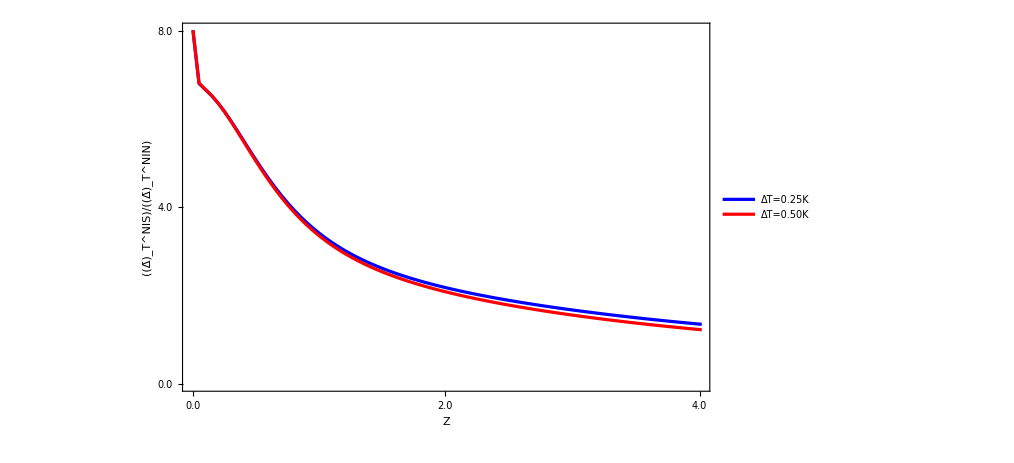

```mathematica
ListLinePlot[{dataQsh0c,dataQsh1c},Frame->True,PlotRange->{{0.0165,4},{0,8.01}},Frame->True,FrameLabel->{Style["Z",25,Bold,Black],Rotate[Style["((Δ̄)_T^NIS)/((Δ̄)_T^NIN)",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],PlotLegends->Placed[{Style["ΔT=0.25K",22,Black,Bold],Style["ΔT=0.50K",22,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.01,"0.0"},{4,"4.0"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0.0165,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},ImageSize->750,PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[rdtg,Scaled[{0.5,0.4}],Scaled[{0,0}],2.5],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

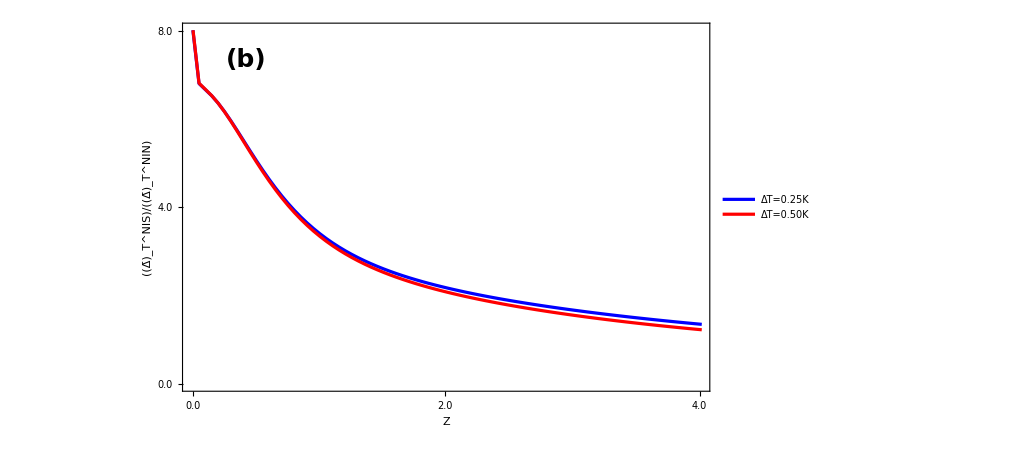

## Ratio of charge shot noise in NIS/NIN

```mathematica
Rshncz=Table[Flatten[{Import["QT1.dat"][[x]][[1]],Import["QT1.dat"][[x]][[4]]/Import["QT1.dat"][[x]][[5]]}],{x,1,41,1}]
```

{{0.0165,16.0815},{0.1165,12.846},{0.2165,11.3185},{0.3165,9.43165},{0.4165,7.55082},{0.5165,5.90628},{0.6165,4.57789},{0.7165,3.5525},{0.8165,2.7788},{0.9165,2.19955},{1.0165,1.76516},{1.1165,1.43696},{1.2165,1.18631},{1.3165,0.9925},{1.4165,0.840692},{1.5165,0.720236},{1.6165,0.623456},{1.7165,0.544773},{1.8165,0.480089},{1.9165,0.426361},{2.0165,0.381304},{2.1165,0.343183},{2.2165,0.310666},{2.3165,0.28272},{2.4165,0.258534},{2.5165,0.237469},{2.6165,0.219013},{2.7165,0.202754},{2.8165,0.188356},{2.9165,0.175547},{3.0165,0.164102},{3.1165,0.153832},{3.2165,0.144583},{3.3165,0.136222},{3.4165,0.12864},{3.5165,0.121742},{3.6165,0.115448},{3.7165,0.109688},{3.8165,0.104405},{3.9165,0.0995466},{4.0165,0.095068}}

```mathematica
Rshncz={{0.0165,16.081455158284406},{0.1165/2,14.846023251675643},{0.1165,12.846023251675643},{0.21650000000000003,11.318515558860751},{0.3165,9.431647742273196},{0.41650000000000004,7.550816110073689},{0.5165000000000001,5.906276041193821},{0.6165,4.577892835702722},{0.7165,3.552504071684621},{0.8165,2.7787997201933625},{0.9165,2.1995537257523354},{1.0165,1.765161030672802},{1.1165,1.4369570588225071},{1.2165000000000001,1.1863063678309194},{1.3165000000000002,0.9925003258907014},{1.4165,0.840692094110761},{1.5165000000000002,0.720235647099813},{1.6165,0.6234559656569308},{1.7165000000000001,0.5447730857115332},{1.8165,0.4800889636537421},{1.9165,0.42636077471620665},{2.0165,0.38130366253714615},{2.1165000000000003,0.34318262407185446},{2.2165000000000004,0.3106657134713898},{2.3165000000000004,0.2827195787077339},{2.4165000000000005,0.25853440641281017},{2.5165000000000006,0.23746945767454483},{2.6165000000000003,0.21901314859955845},{2.7165000000000004,0.20275350070674553},{2.8165000000000004,0.1883560550418476},{2.9165000000000005,0.1755472095094612},{3.0165,0.16410153378961326},{3.1165000000000003,0.15383202832894213},{3.2165000000000004,0.14458258184101033},{3.3165000000000004,0.1362220846783905},{3.4165000000000005,0.1286397996985441},{3.5165,0.12174169568098228},{3.6165000000000003,0.11544752314751318},{3.7165000000000004,0.1096884669674256},{3.8165000000000004,0.10440525020573105},{3.9165000000000005,0.0995465933562002},{4.0165,0.0950679552516762}}
```

{{0.0165,16.0815},{0.05825,14.846},{0.1165,12.846},{0.2165,11.3185},{0.3165,9.43165},{0.4165,7.55082},{0.5165,5.90628},{0.6165,4.57789},{0.7165,3.5525},{0.8165,2.7788},{0.9165,2.19955},{1.0165,1.76516},{1.1165,1.43696},{1.2165,1.18631},{1.3165,0.9925},{1.4165,0.840692},{1.5165,0.720236},{1.6165,0.623456},{1.7165,0.544773},{1.8165,0.480089},{1.9165,0.426361},{2.0165,0.381304},{2.1165,0.343183},{2.2165,0.310666},{2.3165,0.28272},{2.4165,0.258534},{2.5165,0.237469},{2.6165,0.219013},{2.7165,0.202754},{2.8165,0.188356},{2.9165,0.175547},{3.0165,0.164102},{3.1165,0.153832},{3.2165,0.144583},{3.3165,0.136222},{3.4165,0.12864},{3.5165,0.121742},{3.6165,0.115448},{3.7165,0.109688},{3.8165,0.104405},{3.9165,0.0995466},{4.0165,0.095068}}

```mathematica
Rshncz1=Table[Flatten[{Import["QT01.dat"][[x]][[1]],Import["QT01.dat"][[x]][[4]]/Import["QT01.dat"][[x]][[5]]}],{x,1,41,1}]
```

{{0.0165,16.0477},{0.1165,12.8395},{0.2165,11.3142},{0.3165,9.42937},{0.4165,7.55013},{0.5165,5.90658},{0.6165,4.57869},{0.7165,3.55347},{0.8165,2.77977},{0.9165,2.20044},{1.0165,1.76594},{1.1165,1.43762},{1.2165,1.18687},{1.3165,0.992974},{1.4165,0.841089},{1.5165,0.720568},{1.6165,0.623734},{1.7165,0.545006},{1.8165,0.480283},{1.9165,0.426522},{2.0165,0.381437},{2.1165,0.343293},{2.2165,0.310755},{2.3165,0.282791},{2.4165,0.258591},{2.5165,0.237513},{2.6165,0.219044},{2.7165,0.202774},{2.8165,0.188368},{2.9165,0.175551},{3.0165,0.164098},{3.1165,0.153821},{3.2165,0.144566},{3.3165,0.1362},{3.4165,0.128613},{3.5165,0.12171},{3.6165,0.115412},{3.7165,0.10965},{3.8165,0.104363},{3.9165,0.0995011},{4.0165,0.0950196}}

```mathematica
Rshncz1={{0.0165,16.047668667591456},{0.1165/2,14.839451362695584},{0.1165,12.839451362695584},{0.21650000000000003,11.314173013582616},{0.3165,9.42937135312353},{0.41650000000000004,7.55012837453722},{0.5165000000000001,5.906575576120145},{0.6165,4.578686157582507},{0.7165,3.5534715527309637},{0.8165,2.7797667370192656},{0.9165,2.2004396474311685},{1.0165,1.7659376758844965},{1.1165,1.4376222536903287},{1.2165000000000001,1.1868691975845473},{1.3165000000000002,0.9929736309284531},{1.4165,0.8410889704762262},{1.5165000000000002,0.720568003106933},{1.6165,0.6237340707231555},{1.7165000000000001,0.5450055640352929},{1.8165,0.4802829638977715},{1.9165,0.42652218996481106},{2.0165,0.3814373457623276},{2.1165000000000003,0.34329257834929483},{2.2165000000000004,0.31075525176478136},{2.3165000000000004,0.2827914546531274},{2.4165000000000005,0.25859091991651684},{2.5165000000000006,0.23751253961351987},{2.6165000000000003,0.21904442860087686},{2.7165000000000004,0.20277436140513488},{2.8165000000000004,0.18836767560275994},{2.9165000000000005,0.17555060065268518},{3.0165,0.1640975660832418},{3.1165000000000003,0.15382145514617285},{3.2165000000000004,0.14456605807233627},{3.3165000000000004,0.13620018205629106},{3.4165000000000005,0.12861301940790157},{3.5165,0.12171047878534501},{3.6165000000000003,0.11541225925000723},{3.7165000000000004,0.10964950143822924},{3.8165000000000004,0.10436289024047563},{3.9165000000000005,0.09950111307647508},{4.0165,0.09501960001717365}}
```

{{0.0165,16.0477},{0.05825,14.8395},{0.1165,12.8395},{0.2165,11.3142},{0.3165,9.42937},{0.4165,7.55013},{0.5165,5.90658},{0.6165,4.57869},{0.7165,3.55347},{0.8165,2.77977},{0.9165,2.20044},{1.0165,1.76594},{1.1165,1.43762},{1.2165,1.18687},{1.3165,0.992974},{1.4165,0.841089},{1.5165,0.720568},{1.6165,0.623734},{1.7165,0.545006},{1.8165,0.480283},{1.9165,0.426522},{2.0165,0.381437},{2.1165,0.343293},{2.2165,0.310755},{2.3165,0.282791},{2.4165,0.258591},{2.5165,0.237513},{2.6165,0.219044},{2.7165,0.202774},{2.8165,0.188368},{2.9165,0.175551},{3.0165,0.164098},{3.1165,0.153821},{3.2165,0.144566},{3.3165,0.1362},{3.4165,0.128613},{3.5165,0.12171},{3.6165,0.115412},{3.7165,0.10965},{3.8165,0.104363},{3.9165,0.0995011},{4.0165,0.0950196}}

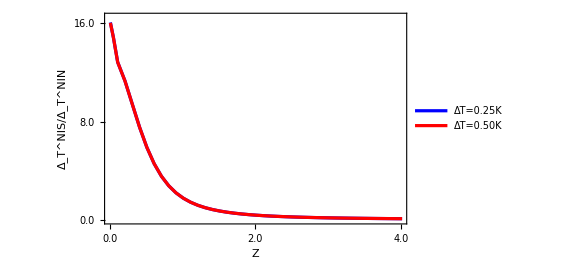

```mathematica
ListLinePlot[{Rshncz,Rshncz1},Frame->True,PlotRange->{{0.0165,4},{0,16.5}},Frame->True,FrameLabel->{Style["Z",19,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",19,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,15],PlotLegends->Placed[{Style["ΔT=0.25K",16,Black,Bold],Style["ΔT=0.50K",16,Black,Bold]},{Right,Top}],FrameTicks->{{{{0.01,"0.0"},{20.06,"0.06"},{8.0,"8.0"},{16.0,"16.0"}},None},{{{0.0165,"0.0"},{2.0, "2.0"},{4,"4.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Red],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

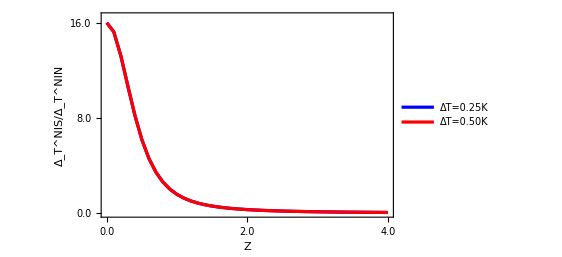

# Quantum Noise NIN and NIS for Z = 0, 1, 3, T2 = 3K as a function of ΔT for applied voltage bias V = 0.0001

```mathematica
T1=3-T/2;
T2=3+T/2;
A=(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2));

(* -(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z)) *)

B=-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2));
u0=Piecewise[{{(1/2*(1+I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1+((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}];

v0=Piecewise[{{(1/2*(1-I((-G^2+ds^2)/G^2)^(1/2)))^(1/2),G^2< ds^2},{(1/2*(1-((G^2-ds^2)/G^2)^(1/2)))^(1/2),G^2> ds^2 }}]; 
Bn=1/(1+Z^2);
kb=8.615*10^-5;
Tc=9.2; 
ds=1.764*kb*Tc;  
Ef=100*ds;
d=1;
a1=kb*T2;
Z=0.0165;  (* 0.01, 1, 3*)
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{V1=0.0000;
f11=1/(1+Exp[(G-V1)/(kb*T1)]);
f12=1/(1+Exp[(G-V1)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
cond1=NIntegrate[(1-Abs[B]^2+Abs[A]^2)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
cond2=NIntegrate[(Bn)df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NS=NIntegrate[(1-Abs[B]^2+Abs[A]^2)(f11(1-f11) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NS=NIntegrate[(Abs[B]^2(1-Abs[B]^2)+Abs[A]^2(1-Abs[A]^2)+2Abs[A]^2*Abs[B]^2)(f11-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qth11NN=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Qsh11NN=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];

list=AppendTo[list1,{T,(2*Re[Qth11NS]+2*Re[Qsh11NS])/(3*kb),(2*Re[Qth11NN]+2*Re[Qsh11NN])/(3*kb),2*Re[Qsh11NS]/(3*kb),2*Re[Qsh11NN]/(3*kb),(2*Re[Qsh11NS]+2*Re[Qth11NS])/(2*Re[Qsh11NN]+2*Re[Qth11NN]),Re[Qsh11NS]/(3*kb*cond1),Re[Qsh11NN]/(3*kb*cond2),(2*Re[Qsh11NS]/(3*kb))/(2*Re[Qsh11NN]/(3*kb)),(Re[Qsh11NS]/(3*kb*cond1))/(Re[Qsh11NN]/(3*kb*cond2))}];},{T,0.001,0.51,0.05}];//AbsoluteTiming
listn=Sort[list1];
Export["check300.dat",listn]
```

{7.42225,Null}

check300.dat

```mathematica
Import["check300.dat"]
```

{{0.001,7.9206,3.99002,1.9851,26.0577,13.1267,1.9851,1.87785×10^-9,1.18837×10^-10,8.70475×10^-9,5.50868×10^-10},{0.101,7.92062,3.99003,1.9851,26.08,13.1378,1.98511,0.0000191554,1.21222×10^-6,0.0000887816,5.61842×10^-6},{0.201,7.92067,3.99003,1.98512,26.1458,13.1709,1.98512,0.0000758578,4.80056×10^-6,0.000351437,0.0000222402},{0.301,7.92077,3.99004,1.98514,26.2552,13.2258,1.98515,0.000170089,0.0000107638,0.000787433,0.0000498316},{0.401,7.9209,3.99004,1.98517,26.4083,13.3026,1.98519,0.000301814,0.0000190999,0.00139587,0.000088336},{0.501,7.92107,3.99005,1.9852,26.6049,13.4014,1.98524,0.000470985,0.0000298056,0.00217551,0.000137674},{0.601,7.92127,3.99007,1.98525,26.8452,13.522,1.9853,0.000677541,0.0000428772,0.00312475,0.000197745},{0.701,7.92152,3.99008,1.9853,27.129,13.6645,1.98537,0.000921406,0.0000583099,0.00424165,0.000268427},{0.801,7.9218,3.9901,1.98536,27.4565,13.8288,1.98545,0.00120249,0.0000760981,0.00552394,0.000349575},{0.901,7.92212,3.99012,1.98543,27.8275,14.0151,1.98553,0.0015207,0.0000962353,0.00696904,0.000441026},{1.001,7.92247,3.99014,1.98551,28.2421,14.2233,1.98563,0.00187591,0.000118714,0.00857402,0.000542595}}

```mathematica
Import["check301.dat"]
```

{{0.001,0.888889,2.,0.444445,2.92433,6.57974,0.444445,1.88732×10^-8,1.19432×10^-8,8.74866×10^-8,5.53626×10^-8},{0.101,0.889082,2.00012,0.444514,2.92771,6.58589,0.444542,0.00019252,0.000121829,0.000892294,0.000564655},{0.201,0.889651,2.00048,0.444718,2.93771,6.60412,0.444829,0.000762405,0.000482459,0.00353209,0.00223515},{0.301,0.890599,2.00108,0.445059,2.95432,6.63442,0.445302,0.00170947,0.00108177,0.00791405,0.00500811},{0.401,0.891922,2.00192,0.445534,2.97755,6.67678,0.445955,0.00303336,0.00191955,0.0140292,0.00887782},{0.501,0.893623,2.003,0.446143,3.00736,6.7312,0.44678,0.0047336,0.00299548,0.0218648,0.0138363},{0.601,0.895699,2.00431,0.446886,3.04376,6.79766,0.447765,0.00680958,0.00430919,0.0314051,0.0198735},{0.701,0.89815,2.00586,0.447763,3.08671,6.87615,0.448901,0.00926054,0.00586018,0.0426304,0.0269771},{0.801,0.900975,2.00765,0.448771,3.1362,6.96667,0.450173,0.0120856,0.00764791,0.0555181,0.0351325},{0.901,0.904173,2.00967,0.449911,3.1922,7.06918,0.451566,0.0152837,0.00967171,0.0700419,0.0443234},{1.001,0.907743,2.01193,0.45118,3.25468,7.18368,0.453067,0.0188537,0.0119309,0.0861727,0.0545312}}

```mathematica
Import["check302.dat"]
```

{{0.001,0.0221607,0.4,0.0554017,0.0729057,1.31595,0.0554017,5.27873×10^-10,4.29956×10^-9,2.44695×10^-9,1.99305×10^-8},{0.101,0.0221661,0.400044,0.0554091,0.0729927,1.31727,0.0554121,5.38467×10^-6,0.0000438585,0.0000249569,0.000203276},{0.201,0.022182,0.400174,0.0554309,0.07325,1.32118,0.0554427,0.000021324,0.000173685,0.0000987905,0.000804655},{0.301,0.0222085,0.400389,0.0554672,0.0736775,1.32769,0.0554932,0.0000478127,0.000389438,0.000221351,0.00180292},{0.401,0.0222455,0.400691,0.0555179,0.0742751,1.33678,0.0555628,0.0000848412,0.000691037,0.000392387,0.00319601},{0.501,0.0222931,0.401078,0.0555828,0.0750422,1.34845,0.0556506,0.000132396,0.00107837,0.000611547,0.00498108},{0.601,0.0223511,0.401551,0.055662,0.0759786,1.36271,0.0557554,0.00019046,0.00155131,0.000878382,0.00715447},{0.701,0.0224197,0.40211,0.0557551,0.0770836,1.37955,0.055876,0.000259012,0.00210967,0.00119235,0.00971174},{0.801,0.0224987,0.402753,0.0558622,0.0783566,1.39895,0.0560108,0.000338027,0.00275325,0.00155281,0.0126477},{0.901,0.0225881,0.403482,0.0559831,0.0797969,1.42093,0.0561583,0.000427476,0.00348182,0.00195903,0.0159564},{1.001,0.022688,0.404295,0.0561174,0.0814036,1.44546,0.0563167,0.000527327,0.00429511,0.0024102,0.0196312}}

## Quantum noise in NIN setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

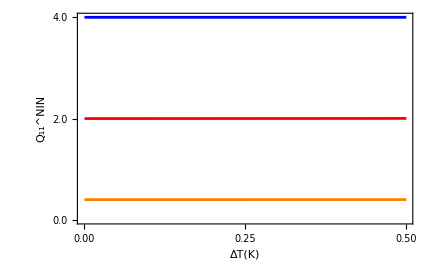

```mathematica
data1cn=Import["check300.dat"][[All,{1,3}]];
data2cn=Import["check301.dat"][[All,{1,3}]];
data3cn=Import["check302.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Q_11^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{2.00,"2.0"},{4,"4.0"},{7,"7.0"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,(*Royal Blue*)Red,(*Crimson*)Orange        (*Dark Orange*)},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

## Quantum noise in NIS setup for Z = (0, 1, 3) and T2 = 3 with respect to ΔT

```mathematica
data1cs=Import["check300.dat"][[All,{1,2}]];
data2cs=Import["check301.dat"][[All,{1,2}]];
data3cs=Import["check302.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
```

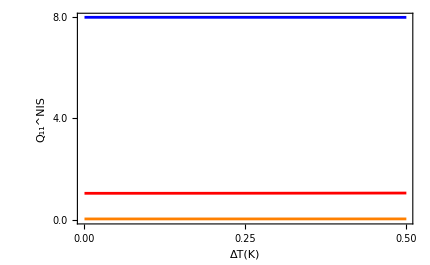

```mathematica
A2=ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Q_11^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0"},{4,"4.0"},{8,"8.0"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

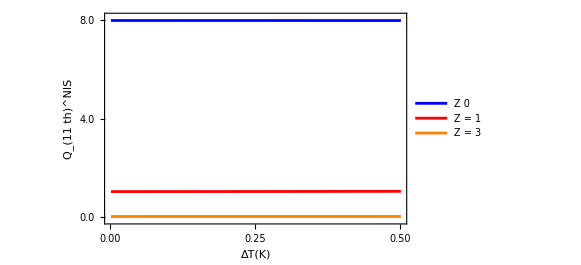

```mathematica
ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->{-0.1,8.1},Frame->True,
PlotLegends->Placed[{"Z  0","Z = 1","Z = 3"},Scaled[{0.88,0.4}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Q_(11  th)^NIS",19,Bold,Black]},
FrameTicksStyle->Directive["Label",Black,Bold,15],
FrameTicks->{{{{0.0,"0.0"},{4.0,"4.0"},{8.0,"8.0"}},None},{{{0,"0.00"},{0.25, "0.25"},{0.5,"0.50"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,19],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.26,0.46}],Scaled[{0,0}],0.35],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

## Δ_T noise NIN

```mathematica
data1cn=Import["check300.dat"][[All,{1,5}]];
data2cn=Import["check301.dat"][[All,{1,5}]];
data3cn=Import["check302.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
```

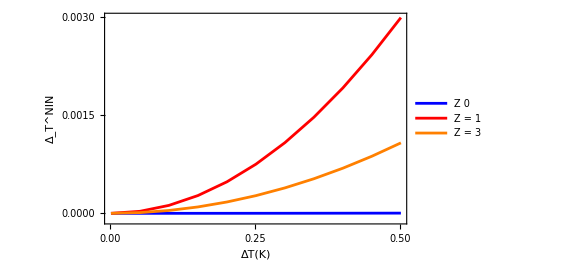

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.003},Frame->True,
PlotLegends->Placed[{"Z  0","Z = 1","Z = 3"},Scaled[{0.2,0.3}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0000"},{0.0015,"0.0015"},{0.003,"0.0030"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.005},Frame->True,
PlotLegends->Placed[{"Z  0","Z = 1","Z = 3"},Scaled[{0.2,0.3}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.0000"},{0.0025,"0.0025"},{0.005,"0.0050"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.4,0.6}],Scaled[{0,0}],0.3],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

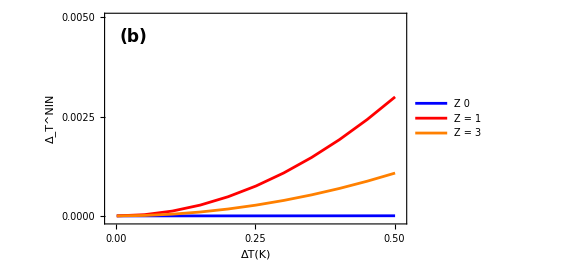

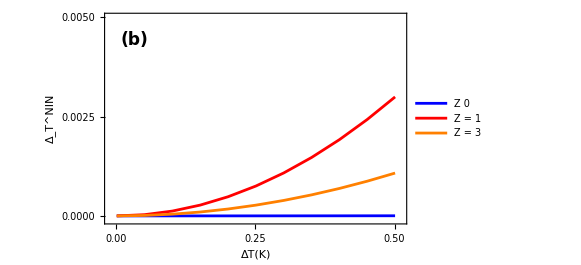

## Δ_T noise NIS

```mathematica
data1cn=Import["check300.dat"][[All,{1,4}]];
data2cn=Import["check301.dat"][[All,{1,4}]];
data3cn=Import["check302.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
```

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.006},Frame->True,
PlotLegends->Placed[{"Z  0","Z = 1","Z = 3"},Scaled[{0.2,0.3}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.000"},{0.003,"0.003"},{0.006,"0.006"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

-Graphics-

```mathematica
ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.010},Frame->True,
PlotLegends->Placed[{"Z  0","Z = 1","Z = 3"},Scaled[{0.2,0.3}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIS",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{0.0,"0.000"},{0.01,"0.010"},{0.005,"0.005"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15],Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A2,Scaled[{0.35,0.6}],Scaled[{0,0}],0.3],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```

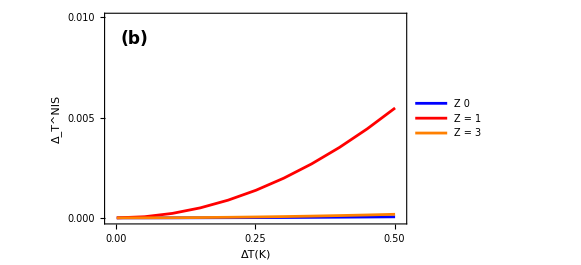

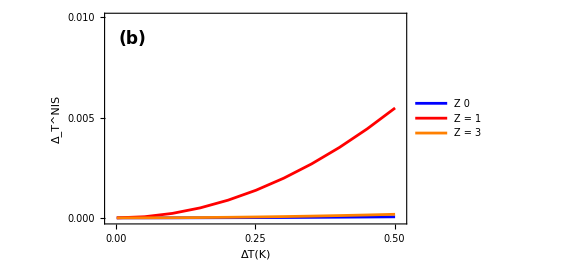

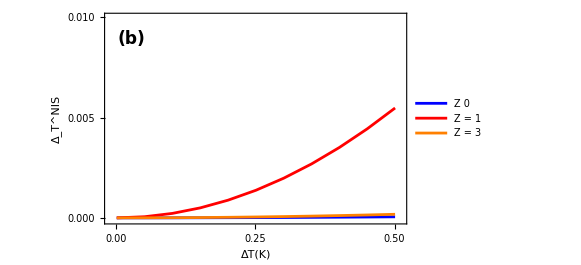

## (Δ̄)_T^NIN

```mathematica
data1cn=Import["check300.dat"][[All,{1,8}]];
data2cn=Import["check301.dat"][[All,{1,8}]];
data3cn=Import["check302.dat"][[All,{1,8}]];
Needs["PlotLegends`"]
```

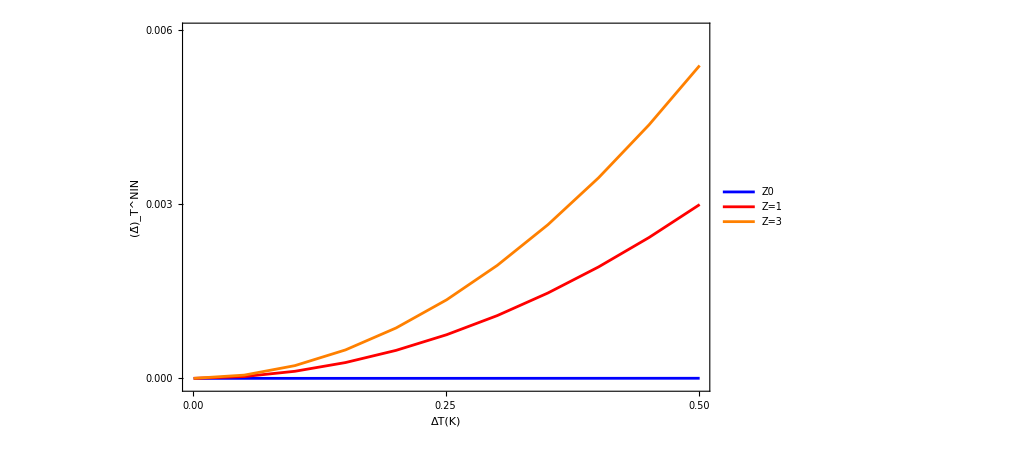

```mathematica
DGnT=ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.006},Frame->True,
PlotLegends->Placed[{Style["Z0",22,Black,Bold],Style["Z=1",22,Black,Bold],Style["Z=3",22,Black,Bold]},Scaled[{0.2,0.6}] ],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Rotate[Style["(Δ̄)_T^NIN",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],ImageSize->750,FrameTicks->{{{{0.0,"0.000"},{0.003,"0.003"},{0.006,"0.006"},{0.25,"0.25"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{3,"3.0"},{0.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},LabelStyle->Directive[Bold,Black,15]]
```

## (Δ̄)_T^NIS

```mathematica
data1cn=Import["check300.dat"][[All,{1,7}]];
data2cn=Import["check301.dat"][[All,{1,7}]];
data3cn=Import["check302.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
```

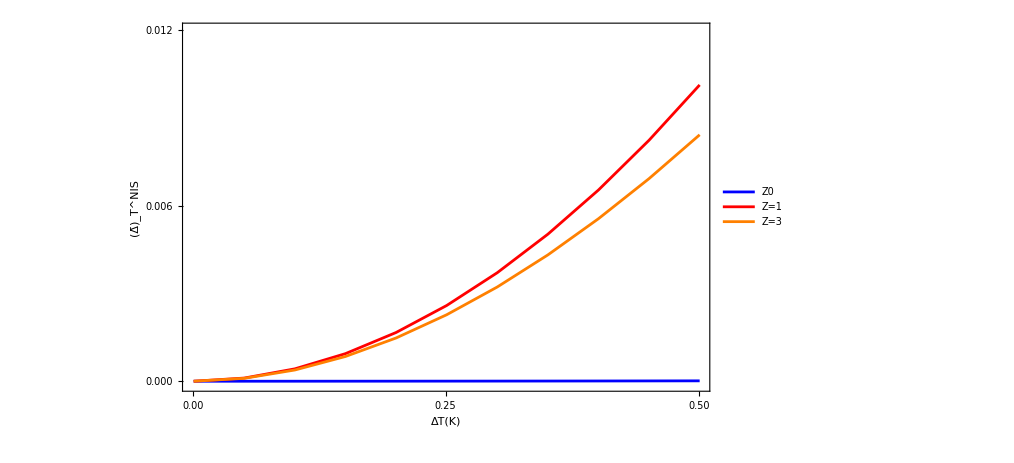

```mathematica
DGsT=ListLinePlot[{data1cn,data2cn,data3cn},Frame->True,PlotRange->{-0.0001,0.012},Frame->True,
PlotLegends->Placed[{Style["Z0",22,Black,Bold],Style["Z=1",22,Black,Bold],Style["Z=3",22,Black,Bold]},Scaled[{0.2,0.5}] ],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Rotate[Style["(Δ̄)_T^NIS",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],ImageSize->750,FrameTicks->{{{{0.0,"0.000"},{0.012,"0.012"},{0.006,"0.006"},{1.005,"0.5"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},LabelStyle->Directive[Bold,Black,16]]
```

## Ratio of Δ_T noise in NIS/NIN

```mathematica
data1cs=Import["check300.dat"][[All,{1,9}]];
data2cs=Import["check301.dat"][[All,{1,9}]];
data3cs=Import["check302.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
```

```mathematica
rdt=ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,
PlotLegends->Placed[{Style["Z0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},Scaled[{0.2,0.5}] ],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Rotate[Style["Δ_T^NIS/Δ_T^NIN",19,Bold,Black],270 Degree]},ImageSize->430,FrameTicksStyle->Directive["Label",Black,Bold,16,Thick],FrameTicks->{{{{0.0,"0.0"},{8,"8.0"},{16,"16.0"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

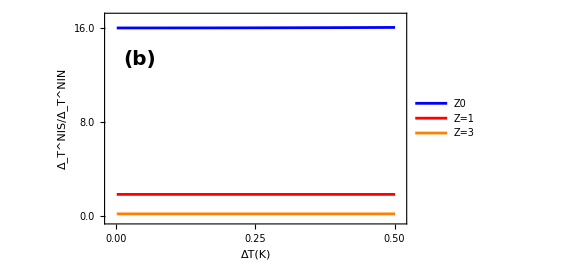

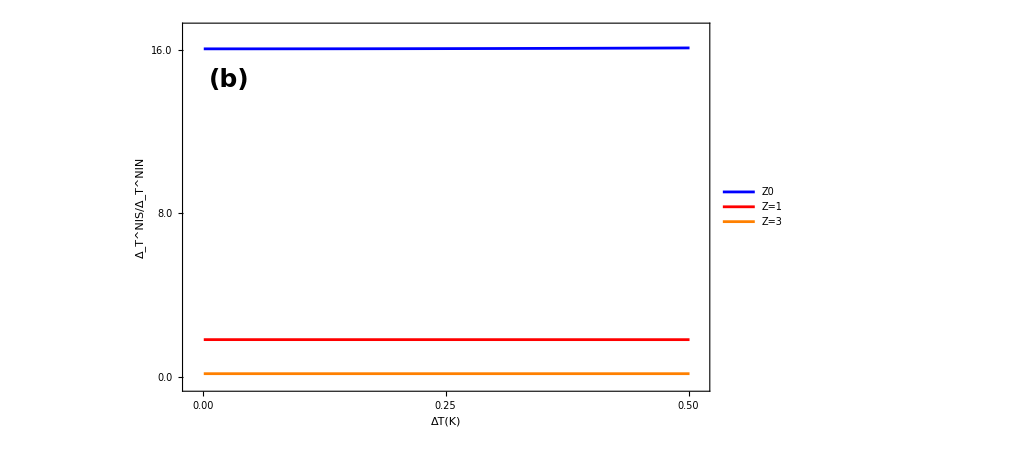

## ((Δ̄)_T^NIS)/((Δ̄)_T^NIN)

```mathematica
data1cs=Import["check300.dat"][[All,{1,10}]];
data2cs=Import["check301.dat"][[All,{1,10}]];
data3cs=Import["check302.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
```

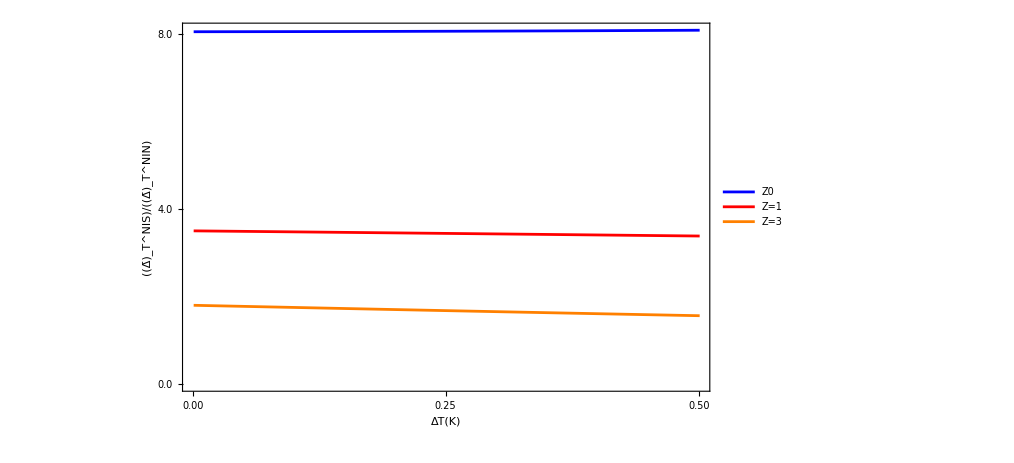

```mathematica
rdtg=ListLinePlot[{data1cs,data2cs,data3cs},Frame->True,PlotRange->All,Frame->True,
PlotLegends->Placed[{Style["Z0",22,Black,Bold],Style["Z=1",22,Black,Bold],Style["Z=3",22,Black,Bold]},Scaled[{0.2,0.6}] ],FrameLabel->{Style["ΔT(K)",25,Bold,Black],Rotate[Style["((Δ̄)_T^NIS)/((Δ̄)_T^NIN)",25,Bold,Black],270 Degree]},FrameTicksStyle->Directive["Label",Black,Bold,22,Thick],ImageSize->750,FrameTicks->{{{{0.0,"0.0"},{8,"8.0"},{4,"4.0"}},None},{{{1,"1.0"},{0,"0.00"},{.5, "0.50"},{.25,"0.25"}},None}},PlotStyle->{Blue,Red,Orange},ImageSize->430,LabelStyle->Directive[Bold,Black,15]]
```

# Figures for paper vs Z

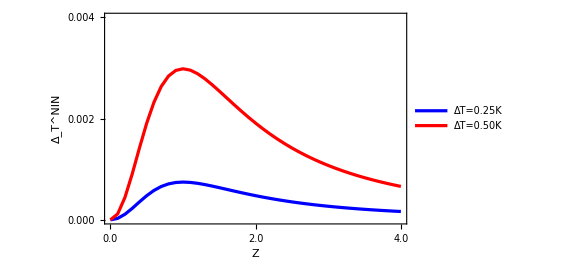

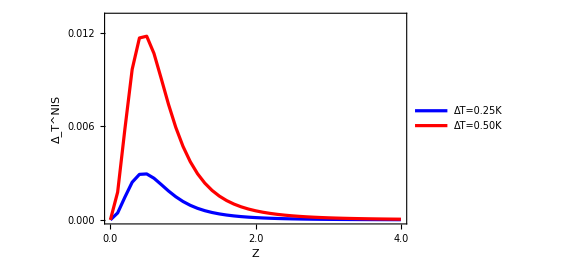

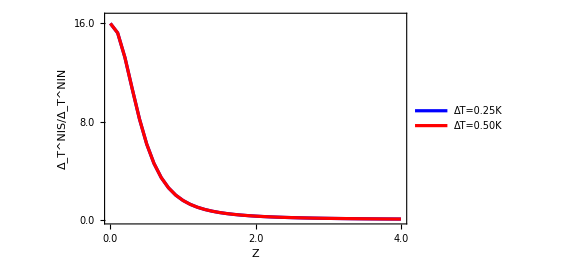

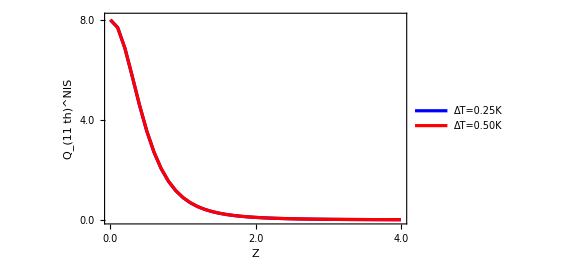

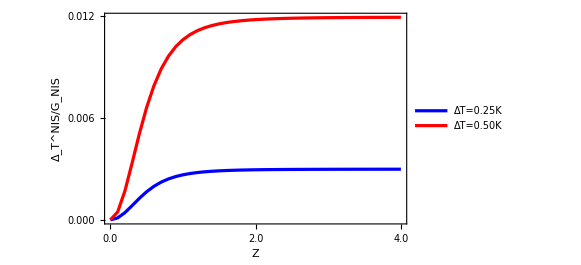

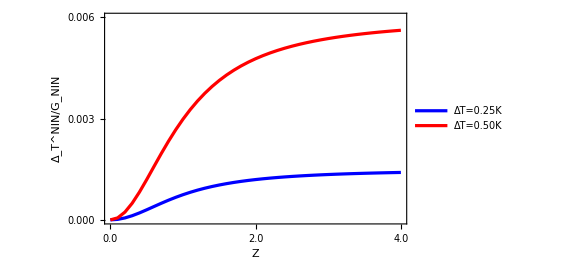

# Figures for paper vs ΔT